# Algebra of Oscilators

```mathematica
rules={
before___·(number_ operator_)·after___/;NumericQ[number]->number(before·operator·after),
before___·(op1_+op2_)·after___:>before·op1·after+before·op2·after,before___·a·SuperDagger[a]·after___:>before·SuperDagger[a]·a·after+before·after,
CenterDot[a_]:>a
};
```

```mathematica
example1=CenterDot@@(RandomInteger[{0,1},{10}]/.{0->a,1->SuperDagger[a]})
```

a·a^†·a^†·a·a·a^†·a·a^†·a·a^†

```mathematica
example2=CenterDot@@Table[RandomSample[{a,SuperDagger[a]},1]⟦1⟧,{10}]
```

a^†·a^†·a·a·a^†·a·a·a·a·a

```mathematica
example3=CenterDot@@(a+RandomInteger[{0,1},{10}](SuperDagger[a]-a))
```

a^†·a·a^†·a^†·a^†·a·a·a·a·a^†

```mathematica
group={before___·a^(n_.)·a^(m_.)->before·a^(n+m),(SuperDagger[a])^(n_.)·(SuperDagger[a])^(m_.)·after___->(SuperDagger[a])^(n+m)·after};
```

```mathematica
example1//.rules//.group/.rules//Expand
```

16 a^†·a+65 (a^†)^2·a^2+55 (a^†)^3·a^3+14 (a^†)^4·a^4+(a^†)^5·a^5

```mathematica
example2//.rules//.group/.rules//Expand
```

2 (a^†)^2·a^6+(a^†)^3·a^7

```mathematica
example3//.rules//.group/.rules//Expand
```

12 (a^†)^3·a^3+8 (a^†)^4·a^4+(a^†)^5·a^5

# Anharmonic Oscilator by Rayleigh-Ritz

```mathematica
Ket[n]
```

|n⟩

Note the unconventional shift. In this section Ket[1] is the ground state, Ket[2] the first excited state etc:

```mathematica
rule={
before___·(number_ operator_)·after___/;NumericQ[number]->number(before·operator·after),
before___·(op1_+op2_)·after___:>before·op1·after+before·op2·after,
CenterDot[a_]:>a,
before___·a·n_->√(n-1)before·n-1,
before___·SuperDagger[a]·n_->√(n+0)before·n+1
};
```

```mathematica
ℙ=(SuperDagger[a]-a)/(√2 I);𝕏=(SuperDagger[a]+a)/(√2);
```

```mathematica
ℙ·ℙ·Ket[n]+𝕏·𝕏·Ket[n]//.rule//Simplify
```

(-1+2 n) |n⟩

```mathematica
Hket=ℙ·ℙ·Ket[n]+0𝕏·𝕏·Ket[n]+𝕏·𝕏·𝕏·𝕏·Ket[n]//.rule//Collect[#,c_Ket,FullSimplify]&
```

1/4 √(-4+n) √(-3+n) √(-2+n) √(-1+n) |-4+n⟩+(-2+n)^(3/2) √(-1+n) |-2+n⟩+1/4 (1-2 n+6 n^2) |n⟩+n^(3/2) √(1+n) |2+n⟩+1/4 √n √(1+n) √(2+n) √(3+n) |4+n⟩

```mathematica
(makeMatrix=Cases[Hket,c_  Ket[a_]->({n_,m_}/;(m==a)->c)]/.{n$->n,m$->m})//TableForm
```

{n_,m_}/;m==-4+n→1/4 √(-4+n) √(-3+n) √(-2+n) √(-1+n)
{n_,m_}/;m==-2+n→(-2+n)^(3/2) √(-1+n)
{n_,m_}/;m==n→1/4 (1-2 n+6 n^2)
{n_,m_}/;m==2+n→n^(3/2) √(1+n)
{n_,m_}/;m==4+n→1/4 √n √(1+n) √(2+n) √(3+n)

```mathematica
M=150;
```

```mathematica
H=N[#,50]&@SparseArray[makeMatrix,{M,M}];
```

```mathematica
ArrayPlot[H]
```

-Graphics-

```mathematica
energies=Eigenvalues[H,-10]//Sort
```

{1.0603620904841828996470460167132260732483530402026,3.799673029801394168783094189333327503501119588689,7.4556979379867383921565913605999734583352829350441,11.644745511378162020850373327134371754265207320332,16.261826018850225937894957616685662848293826549241,21.238372918235940024149720244018339656618211679087,26.528471183682518191814006371187254277609145413768,32.098597710968326634274194318232154263052660544519,37.923001027033985146521551776903739669461770800935,43.981158097289730785392927285924410377319640815217}

```mathematica
ϕ[n_,x_]:=(ⅇ^(-x^2/2))/(√(2^(n-1)(n-1)!√π))HermiteH[n-1,x];
```

```mathematica
evs=Eigensystem[H,-10]ᵀ//Sort//Take[#,10]&;
```

```mathematica
basis=(ϕ[#,x]&/@Range[150]);
```

```mathematica
toPlot=Simplify[#⟦2⟧.basis+#⟦1⟧]&/@evs;
```

```mathematica
newPlot=Plot[toPlot,{x,-4,4}];
```

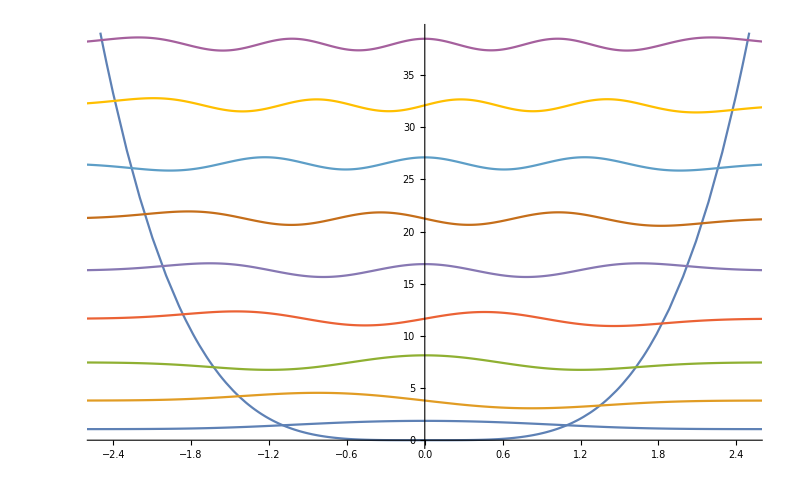

```mathematica
Show[Plot[{x^4},{x,-5/2,5/2}],newPlot]
```

```mathematica
energies//N[#,22]&
```

{1.060362090484182899647,3.799673029801394168783,7.455697937986738392157,11.64474551137816202085,16.26182601885022593789,21.23837291823594002415,26.52847118368251819181,32.09859771096832663427,37.92300102703398514652,43.98115809728973078539}

in perfect agreement with the results from hep-th/9812211:

-Graphics-

# Replacements in Dif Eqs

```mathematica
Schrodinger=-D[ψ[x], {x,2}]+x^2 ψ[x]-(2n-1)ψ[x]
```

-(-1+2 n) ψ[x]+x^2 ψ[x]-ψ''[x]

```mathematica
Schrodinger/.ψ:>(ϕ[n,#]&)//Simplify//FullSimplify
```

0